```mathematica
uTrue[x_,y_]:= 1 + x + y*y
```

```mathematica
epsi=1
```

1

```mathematica
a={{1,0},{0,1}}
b={0,0}
c=0
```

{{1,0},{0,1}}

{0,0}

0

```mathematica
fExpression= -Div[a.Grad[uTrue[x,y],{x,y}]    , {x,y}] + Div[Times[b,uTrue[x,y]],{x,y}] + Times[c,uTrue[x,y]]
```

-2

```mathematica
nANablaU = {1,0}.a.Grad[uTrue[x,y],{x,y}]
```

1

```mathematica
CForm[nANablaU]
```

1

```mathematica
f[x_,y_]:=Evaluate[fExpression]
```

```mathematica
CForm[fExpression]
```

-2

```mathematica
CForm[uTrue[x,y]]
```

1 + x + Power(y,2)

```mathematica
amikel={{epsi Exp[-20 √(x^2+y^2)],0},{0,epsi Exp[-20 √(x^2+y^2)]}}
bmikel={2-y^2,2-x}
cmikel=(1+x) (1+y)^2
```

{{ⅇ^(-20 √(x^2+y^2)),0},{0,ⅇ^(-20 √(x^2+y^2))}}

{2-y^2,2-x}

(1+x) (1+y)^2

```mathematica
VectorPlot[b,{x,0,1},{y,0,1}]
```

-Graphics-

```mathematica
nan=Transpose[{x,y}].a.{x,y}
```

x^2+y^2

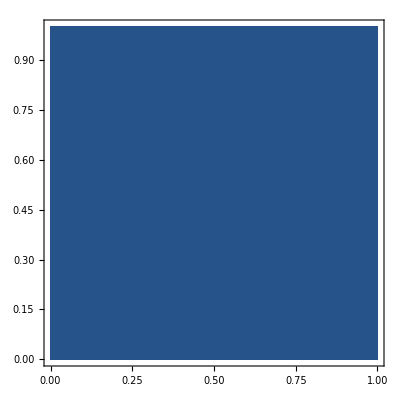

```mathematica
DensityPlot[Transpose[{0,-1}].a.{0,-1},{x,0,1},{y,0,1}]
```

```mathematica
DensityPlot[Transpose[{0,1}].a.{0,1},{x,0,1},{y,0,1}]
```

-Graphics-

```mathematica
DensityPlot[Transpose[{-1,0}].a.{-1,0},{x,0,1},{y,0,1}]
```

-Graphics-